### Spontaneous emission - resonance fluorescence

```mathematica
Δ = 1.0;
Ω = 1.0;
γ = 1.0;
L = √γ σm;
H=Δ/2 σz +Ω σx;
ψ0 = {1,1}/√2;
ts = Range[0,30.0,0.001];
{ψ,jumpList}=QuantumJumpUnravelling[H,{L},ψ0,ts,3];
jumpList
```

{{1256,1},{1629,1},{2520,1},{4481,1},{5229,1},{6286,1},{10396,1},{15117,1},{23262,1},{27175,1}}

```mathematica
ψ
```

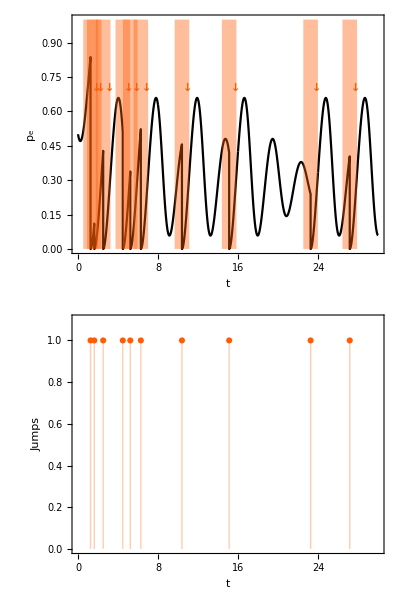

```mathematica
Column[{ListLinePlot[{ts,Abs[ψ⟦All,1⟧]^2}ᵀ,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓"}],
FrameLabel->{Style["t",Italic],"p_e"},
AspectRatio->1/4,
ImageSize->700,
PlotRange->{0,1}
],
ListPlot[Table[{ts[[j[[1]]]],j[[2]]},{j,jumpList}],PlotMarkers->Automatic,PlotRange->{{0,Last@ts},{0,1.1}},Filling->Axis,PlotStyle->COLORLIST[[2]],
AspectRatio->1/4,
ImageSize->700,
FrameLabel->{Style["t",Italic],"Jumps"}
]}]
```

### Ex: Incoherent qubit (“single electron transistor”)

```mathematica
H=σz;
γ = 1;
fL = 0.3;
fR = 0.4;
cops = {√(γ(1-fL))σm,√(γ fL)σp,√(γ(1-fR))σm,√(γ fR)σp};
ψ0 = {1,0};
ts = Range[0,10.0,0.001];
{ψ,jumpList}=QuantumJumpUnravelling[H,cops,ψ0,ts,1];
jumpList
```

{{158,1},{722,4},{1221,3},{3377,2},{3446,3},{3902,2},{4898,1},{5780,4},{5973,1},{7945,4},{8062,1}}

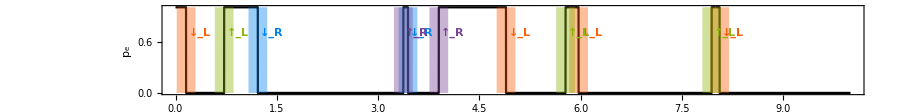

```mathematica
ListLinePlot[{ts,Abs[ψ⟦All,1⟧]^2}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓_L","↑_L","↓_R","↑_R"}],
FrameLabel->{Style["t",Italic],"p_e"},
PlotRange->{-0.1,1.1},
AspectRatio->1/8,
ImageSize->900
]
```

Particle charge (= accumulated particle current up to time t)

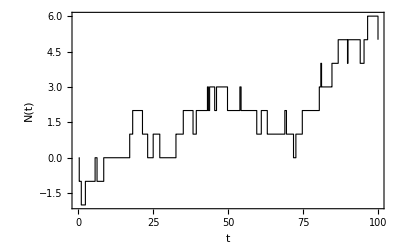

```mathematica
ts = Range[0,100.0,0.001];
{ψ,jumpList}=QuantumJumpUnravelling[H,cops,ψ0,ts,2];

charge={ts⟦jumpList⟦All,1⟧⟧,Accumulate[jumpList⟦All,2⟧/.{1->1,2->-1,3->0,4->0}]}//Transpose;
ListLinePlot[charge,
InterpolationOrder->0,
PlotStyle->Directive[Black,Thickness[0.002](*,Dotted*)],
FrameLabel->{Style["t",Italic],Style["N(t)",Italic]},
ImageSize->{Automatic,200}
]
```

### Ex: 2 qubits connected to a single bath

Two coupled qubits. But only the first is coupled to a bath.

```mathematica
LoadSpinChainMatrices[2];
H = sp[1].sm[2]+sm[1].sp[2] (* Exchange interaction *);
cops = {sm[1],sp[1]} (* Baths only in qubit 1 *);
ts = Range[0,7.0,0.001];
{ψ,jumpList}=QuantumJumpUnravelling[H,cops,{1,0,0,0},ts,4];
jumpList
```

{{1169,1},{1455,2},{2770,1},{3744,2},{3925,1},{5694,1},{6719,2}}

```mathematica
(* Reduced density matrices *)
ρ1 = Table[PTr[out[ψ⟦i⟧,ψ⟦i⟧],{2}],{i,Length@ψ}];
ρ2 = Table[PTr[out[ψ⟦i⟧,ψ⟦i⟧],{1}],{i,Length@ψ}];
```

```mathematica
entanglement = Table[vonNeumann[ρ],{ρ,ρ1}];
occupation = Table[2 Abs[ϕ⟦1⟧]^2+Abs[ϕ⟦2⟧]^2+Abs[ϕ⟦3⟧]^2,{ϕ,ψ}];
```

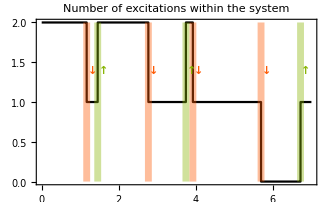
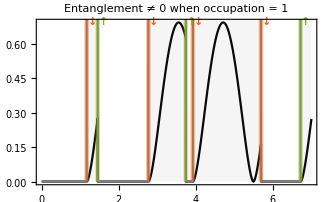

```mathematica
sel = {ts,Round[occupation]/.{2->0}}ᵀ;
Row@{ListLinePlot[{ts,occupation}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓","↑"},0.015,0,2],
PlotLabel->Style["Number of excitations within the system",Black,14]
],
Show[ListLinePlot[{ts,entanglement}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓","↑"},0.01],
PlotLabel->Style["Entanglement ≠ 0 when occupation = 1",14,Black]
],
ListLinePlot[sel,Filling->Axis,PlotStyle->Gray,FillingStyle->Opacity[0.08]]
]}
```

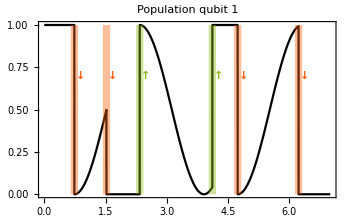
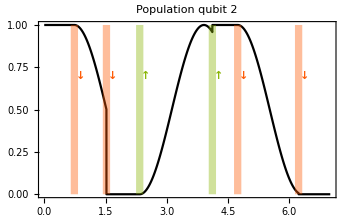

```mathematica
{ListLinePlot[{ts,ρ1⟦All,1,1⟧}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓","↑"}],
ImageSize->350,
PlotLabel->"Population qubit 1"
],
ListLinePlot[{ts,ρ2⟦All,1,1⟧}ᵀ,PlotRange->All,PlotStyle->Black,
Epilog->JumpHighlight[jumpList,ts,{"↓","↑"}],
ImageSize->350,
PlotLabel->"Population qubit 2"
]}
```